```mathematica
u0[x_]:=Piecewise[{{0,-1<x<1},{20,x<-1},{20,x>1}}]
Plot[u0[x]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[u0[x]]

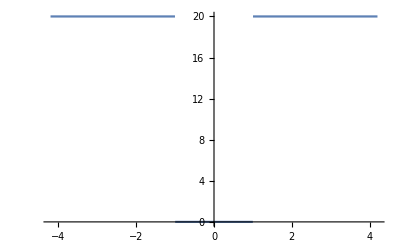

```mathematica
Plot[Piecewise[{{0,-1<x<1},{20,x<-1||x>1}},0],{x,-4.2,4.2}]
```

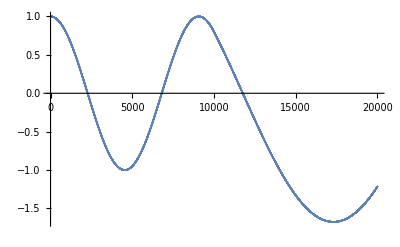

Part::pkspec1: The expression {1, 1, 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., «19950»} cannot be used as a part specification. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/Part",
ButtonNote->"Part::pkspec1"]

```mathematica
totalx=2;
deltax=.0001;
num=totalx/deltax;
ψ=Table[0,{i,num}];
e=24;
ψ[[1]]=1;
ψ[[2]]=1;
For[i=2,i<num,i++,ψ[[i+1]]=2ψ[[i]]-ψ[[i-1]]+2deltax^2(u0[i deltax]-e)ψ[[i]]]
p1=ListPlot[ψ]
```